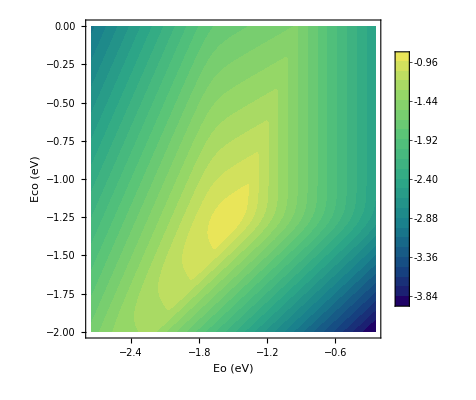

```mathematica
k=8.617343*(10^-5);
h=4.13566743*(10^-15);
T=600;
pco=0.67;
po2=0.33;
ETS3=1.39*Eo+1.56;
ETS4=0.7*(Eo+Eco)+0.02;
Eo2=0.89*Eo+0.17;
Ea3=Max[ETS3-Eo2,0];
Ea4=Max[ETS4-(Eo+Eco),0];
S1=-20.522176*(10^-4);
S2=-21.2625*(10^-4);
S3=0;
S4=22.1906*(10^-4);
K1=Exp[-(Eco-T S1)/(k T)];
K2=Exp[-(Eo2-T S2)/(k T)];
cita=1/(1+K1*pco+K2*po2);
citaco=K1 pco cita;
citao2=K2 po2 cita;
v=k T/h;
k3=v Exp[-(Ea3)/(k T)];
k4=v Exp[-(Ea4)/(k T)];
r3=k3 citao2 cita;
r4=k4 citaco;
rs=Min[2 r3,r4];
As=k T Log[rs/v];
Plot1=ContourPlot[As,{Eo,-2.75,-0.25},{Eco,-2,0},PlotLegends->Automatic,Exclusions->None,ContourStyle->None, Contours->25,ColorFunction->"BlueGreenYellow",ContourStyle->None,PlotTheme-> "Web",FrameLabel->{Style["Eo (eV)",Large,Black],Style["Eco (eV)",Large,Black]},LabelStyle->Directive[Medium,Black],Exclusions->None]
```